```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{4,3,2,4,2,0,2,2,4,3,2,28},{5,4,4,6,2,2,2,2,1,3,4,35},{5,0,1,0,1,0,2,1,1,1,2,14},{5,3,2,2,0,0,2,0,0,0,0,14},{4,3,2,1,2,2,3,0,3,3,2,25},{3,3,0,6,1,1,2,0,2,3,0,21},{5,4,3,5,1,3,3,2,2,3,2,33},{6,2,4,1,2,0,2,1,4,3,1,26},{6,3,4,0,1,0,3,1,0,3,4,25},{6,2,4,1,0,1,2,0,1,3,0,20},{3,4,3,6,1,2,4,2,3,3,3,34},{6,4,4,5,2,2,2,2,4,0,2,33},{5,3,3,2,0,0,2,2,2,3,2,24},{4,2,3,1,2,2,3,0,0,3,3,23},{4,3,4,4,1,3,3,2,3,3,2,32},{5,3,4,3,1,2,2,1,0,3,3,27},{5,4,4,3,1,0,2,2,1,3,2,27},{4,4,4,2,1,2,3,2,1,2,3,28},{4,2,4,4,2,1,3,1,1,3,2,27},{5,4,3,3,2,2,3,2,2,3,4,33},{2,2,3,4,1,3,3,1,3,3,2,27},{6,3,4,4,2,1,2,1,2,3,3,31},{5,4,3,5,2,1,3,2,2,3,2,32},{6,4,4,6,2,3,4,2,4,3,3,41},{6,4,4,6,2,1,4,1,3,3,2,36},{6,3,4,6,2,2,3,1,4,3,3,37},{4,2,4,2,2,1,3,0,3,3,1,25},{5,0,0,0,0,2,0,0,0,0,1,8},{5,2,4,2,2,2,3,2,1,3,4,30},{3,0,2,1,0,3,2,0,0,1,2,14},{6,3,4,6,2,2,3,2,1,3,4,36},{6,4,4,6,2,2,3,2,4,3,4,40},{5,3,4,2,1,1,2,1,2,2,3,26}};
scores=Transpose[grades];
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{Length[scores],Length[scores]}];
For[i=1,i≤Length[scores],i++,
For[j=1,j≤Length[scores],j++,
corr[[i]][[j]]=N[Correlation[scores[[i]],scores[[j]]]];
]
]
```

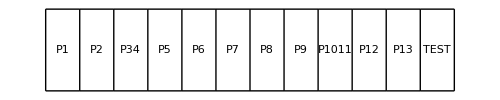
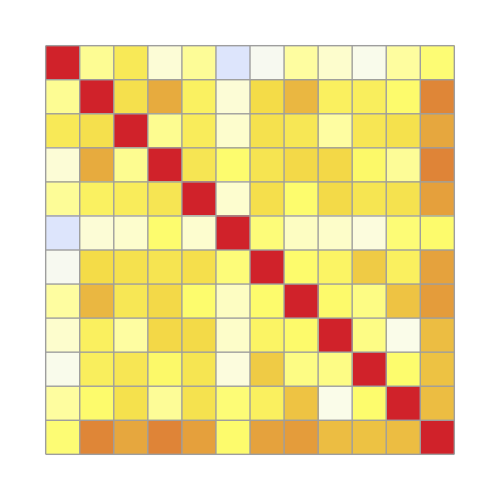
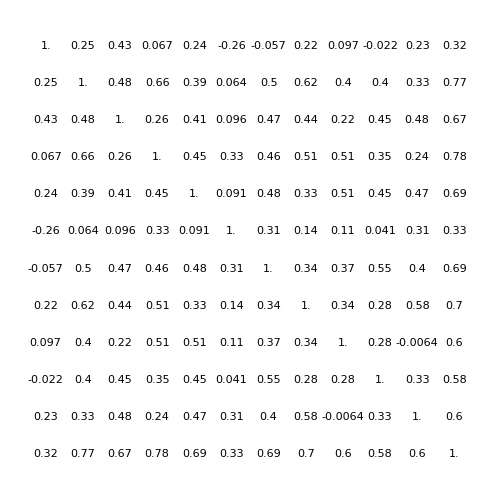
-Graphics-
-Graphics--Graphics--Graphics-

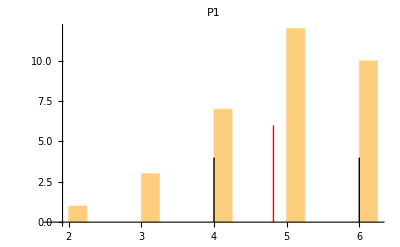
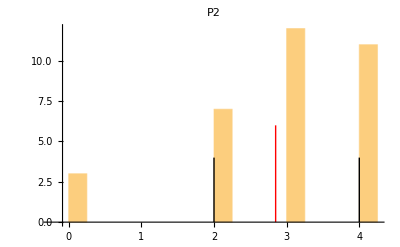
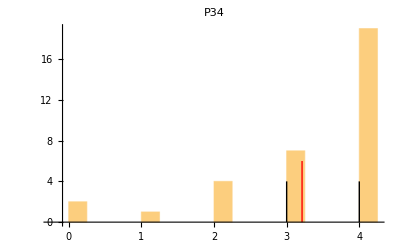
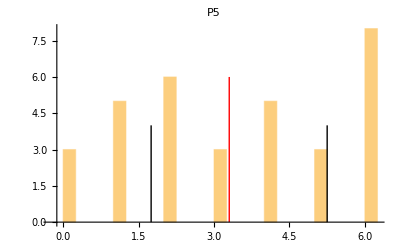
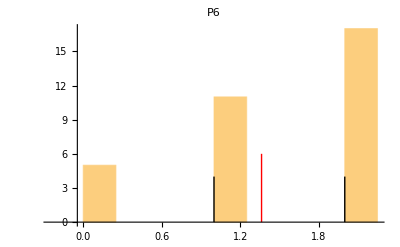
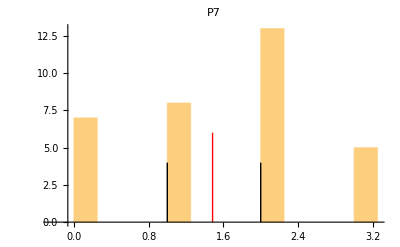
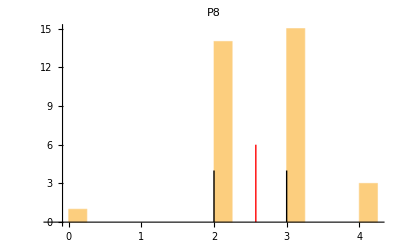
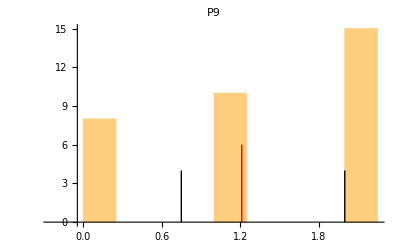

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P34,P5,P6,P7,P8,P9,P1011,P12,P13,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->42,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms,for,each,problem,&,test,as,a,whole*)
histograms={};
For[i=1,i≤Length[scores],i++,
histograms=Append[histograms,Histogram[scores[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[scores[[i]]],0},{Mean[scores[[i]]],6}}],{Directive[{Thick,Black}],Line[{{Quartiles[scores[[i]]][[1]],0},{Quartiles[scores[[i]]][[1]],4}}],Line[{{Quartiles[scores[[i]]][[3]],0},{Quartiles[scores[[i]]][[3]],4}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[Length[histograms]]]
```

```mathematica
(*range of scores: 20 to 37*)
(*this is where we'll draw the D to A range (traditionally: 60 to 100)*)
```